```mathematica
PD1[x_,y_,z_,d_]= (Cos[x]Sin[y])^2+Cos[z]^2Sin[x]^2 Cos[y]^2+(Sin[2 x]Sin[2y]Cos[z]Cos[d])/2
```

Cos[y]^2 Cos[z]^2 Sin[x]^2+Cos[x]^2 Sin[y]^2+1/2 Cos[d] Cos[z] Sin[2 x] Sin[2 y]

```mathematica
<<MaTeX`
```

```mathematica
Manipulate[Plot3D[PD1[x,y,angulo ,dif],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14], Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{angulo ,0,2Pi},{dif,0,2 Pi}]
```

```mathematica
PD2[x_,y_,z_,d_]=(Cos[x]Cos[y])^2+(Cos[z]Sin[x]Sin[y])^2-(Sin[2 x]Sin[2y]Cos[z]Cos[d])/2
```

Cos[x]^2 Cos[y]^2+Cos[z]^2 Sin[x]^2 Sin[y]^2-1/2 Cos[d] Cos[z] Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[PD2[x,y,z,dif],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{z,0,2Pi},{dif,0,2 Pi}]
```

```mathematica
Pabs[x_,z_]=(Sin[z]Sin[x])^2
```

Sin[x]^2 Sin[z]^2

```mathematica
Plot3D[Pabs[x,z],{x,0,2Pi},{z,0,2 Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, o],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}]
```

-Graphics3D-

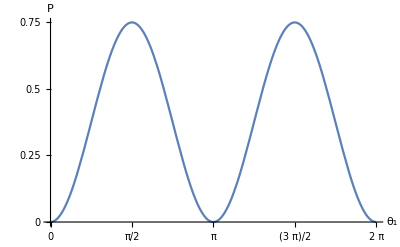

```mathematica
Plot[Pabs[x,Pi/3],{x,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.25,0.5,0.75,1}}]
```

```mathematica
Ahora hagamos las graficas del camino uno
```

```mathematica
P1D1[x_,y_,z_,d_]= (Cos[x]Cos[z]Sin[y])^2+Sin[x]^2 Cos[y]^2+(Sin[2 x]Sin[2y]Cos[z]Cos[d])/2
```

Cos[y]^2 Sin[x]^2+Cos[x]^2 Cos[z]^2 Sin[y]^2+1/2 Cos[d] Cos[z] Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[P1D1[x,y,angulo,dif],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{angulo,0,2Pi},{dif,0,2 Pi}]
```

```mathematica
P1D2[x_,y_,z_,d_]=(Cos[x]Cos[y]Cos[z])^2+(Sin[x]Sin[y])^2-(Sin[2 x]Sin[2y]Cos[z]Cos[d])/2
```

Cos[x]^2 Cos[y]^2 Cos[z]^2+Sin[x]^2 Sin[y]^2-1/2 Cos[d] Cos[z] Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[P1D2[x,y,anglo,dif],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{anglo,0,2Pi},{dif,0,2 Pi}]
```

```mathematica
P1abs[x_,z_]=(Sin[z]Cos[x])^2
```

Cos[x]^2 Sin[z]^2

```mathematica
Plot3D[P1abs[x,z],{x,0,2Pi},{z,0,2 Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, o],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}]
```

-Graphics3D-

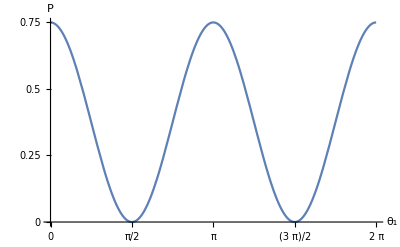

```mathematica
Plot[P1abs[x,Pi/3],{x,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.25,0.5,0.75,1}}]
```

```mathematica
f[w_,t_,β_]=(1+Sign[Sin[w t]])/2+β*(1-Sign[Sin[w t]])/2
```

1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]])

```mathematica
a[w_,t_,α_]=α*(1-Sign[Sin[w t]])/2
```

```mathematica
1/2 α (1-Sign[Sin[t w]])
```

1/2 α (1-Sign[Sin[t w]])

```mathematica
PcD1[w_,t_,d_,x_,y_,β_]=(Cos[x]Sin[y])^2+(f[w,t,β]Sin[x]Cos[y])^2 +(Sin[2 x]Sin[2y]f[w,t,β]Cos[d])/2
```

Cos[y]^2 (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]]))^2 Sin[x]^2+Cos[x]^2 Sin[y]^2+1/2 Cos[d] (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]])) Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[PcD1[w,t,d ,x,y,β],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{β,0,1},{w,0,2Pi},{d,0,2 Pi},{t,0,100}]
```

```mathematica
PcD2[w_,t_,d_,x_,y_,β_]=(Cos[x]Cos[y])^2+(f[w,t,β]Sin[x]Sin[y])^2 -(Sin[2 x]Sin[2y]f[w,t,β]Cos[d])/2
```

Cos[x]^2 Cos[y]^2+(1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]]))^2 Sin[x]^2 Sin[y]^2-1/2 Cos[d] (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]])) Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[PcD2[w,t,d ,x,y,β],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{β,0,1},{w,0,2Pi},{d,0,2 Pi},{t,0,100}]
```

```mathematica
Pcabs1[w_,t_,x_,α_]=(Sin[x])^2  * a[w,t,α]
```

1/2 α (1-Sign[Sin[t w]]) Sin[x]^2

```mathematica
Manipulate[Plot3D[Pcabs1[w,t,x,α],{x,0,2Pi},{α,0,1},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[α,Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1},{0,0.5,1}}],{w,0,100},{t,0,100}]
```

```mathematica
Ahora las del chopper por el otro brazo
```

Ahora brazo chopper del el las otro por

```mathematica
P1cD1[w_,t_,d_,x_,y_,β_]=(Cos[x]Sin[y] f[w,t,β])^2+(Sin[x]Cos[y])^2 +(Sin[2 x]Sin[2y]f[w,t,β]Cos[d])/2
```

Cos[y]^2 Sin[x]^2+Cos[x]^2 (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]]))^2 Sin[y]^2+1/2 Cos[d] (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]])) Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[P1cD1[w,t,d ,x,y,β],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{β,0,1},{w,0,2Pi},{d,0,2 Pi},{t,0,100}]
```

```mathematica
P1cD2[w_,t_,d_,x_,y_,β_]=(Cos[x]Cos[y] f[w,t,β])^2+(Sin[x]Sin[y])^2 -(Sin[2 x]Sin[2y]f[w,t,β]Cos[d])/2
```

Cos[x]^2 Cos[y]^2 (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]]))^2+Sin[x]^2 Sin[y]^2-1/2 Cos[d] (1/2 β (1-Sign[Sin[t w]])+1/2 (1+Sign[Sin[t w]])) Sin[2 x] Sin[2 y]

```mathematica
Manipulate[Plot3D[P1cD2[w,t,d ,x,y,β],{x,0,2Pi},{y,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[Subscript[θ, 2],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1}}],{β,0,1},{w,0,2Pi},{d,0,2 Pi},{t,0,100}]
```

```mathematica
Pcabs1[w_,t_,x_,α_]=(Cos[x])^2  a[w,t,α]
```

1/2 α Cos[x]^2 (1-Sign[Sin[t w]])

```mathematica
Manipulate[Plot[Pcabs1[w,t,x,α],{x,0,2Pi},AxesLabel->{Style[Subscript[θ, 1],Bold,16],Style[P,Bold,16]},TicksStyle->Directive[ 14],Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{0,0.5,1},{0,0.5,1}}],{w,0,100},{t,0,100},{α,0,1}]
```